# Neural Networks

Use a GPU for training, when available:

```mathematica
SetOptions[NetTrain,TargetDevice->"GPU"];
```

### Balance Scale Example

```mathematica
net=NetGraph[{
CatenateLayer[],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[3],
SoftmaxLayer[]
},{
{NetPort["leftweight"],NetPort["leftdistance"],NetPort["rightweight"],NetPort["rightdistance"]}->1,
1->2->3->4->5->NetPort["balance"]
},
"leftweight"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"leftdistance"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"rightweight"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"rightdistance"-> NetEncoder[{"Class",{1,2,3,4,5},"UnitVector"}],
"balance"->NetDecoder[{"Class",{"L","B","R"}}]
]
```

NetGraph[]

```mathematica
rawdata=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/balance-scale/balance-scale.data","CSV"];
```

```mathematica
training=Dataset[
Map[
AssociationThread[{"balance","leftweight","leftdistance","rightweight","rightdistance"}->#]&,
rawdata]
]
```

Dataset[<>]

```mathematica
result=NetTrain[net,training]
```

NetGraph[]

```mathematica
result[<|"leftweight"->1,"leftdistance"->1,"rightweight"->1,"rightdistance"->1|>]
```

B

```mathematica
result[<|"leftweight"->2,"leftdistance"->1,"rightweight"->1,"rightdistance"->1|>]
```

L

```mathematica
result[<|"leftweight"->2,"leftdistance"->1,"rightweight"->1,"rightdistance"->1|>]
```

L

```mathematica
test=Table[
{leftweight,leftdistance,rightweight,rightdistance}=RandomInteger[{1,5},4];
balance=rightweight*rightdistance-leftweight*leftdistance;
balance=Which[
balance<0,"L",
balance==0,"B",
balance>0,"R"
];
{leftweight,leftdistance,rightweight,rightdistance}->balance,
1000];
```

```mathematica
measurements=ClassifierMeasurements[result,test]
```

ClassifierMeasurementsObject[…]

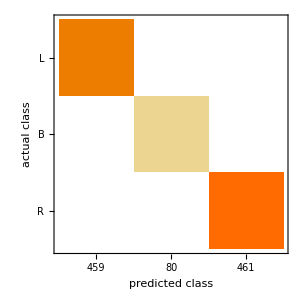

```mathematica
measurements["ConfusionMatrixPlot"]
```

### Car Evaluation Example

Source of the data set:

```mathematica
Hyperlink["http://archive.ics.uci.edu/ml/datasets/Car+Evaluation"]
```

Import the data as a .csv (comma separated file):

```mathematica
rawdata=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/car/car.data","CSV"];
```

The number of rows in the data is 1728:

```mathematica
Length[rawdata]
```

1728

RandomSample lets you examine a few rows of data. Grid lets you format the data as a table. View a random sample of the data:

```mathematica
RandomSample[rawdata,10]//Grid[#,Frame->All,Alignment->Left]&
```

high | low | 4 | 2 | small | low | unacceptable
high | low | 2 | more | big | high | acceptable
high | very high | 5 or more | 2 | small | low | unacceptable
very high | very high | 5 or more | 4 | medium | high | unacceptable
medium | very high | 3 | 2 | medium | medium | unacceptable
low | low | 3 | 2 | big | low | unacceptable
low | low | 3 | more | medium | low | unacceptable
low | low | 5 or more | 4 | small | low | unacceptable
medium | very high | 5 or more | 4 | small | medium | unacceptable
high | low | 5 or more | more | medium | high | acceptable

Translate short abbreviated names to longer more descriptive names:

```mathematica
rawdata=rawdata/.{"vhigh"->"very high","med"->"medium","5more"->"5 or more","unacc"->"unacceptable","acc"->"acceptable","vgood"->"very good"};
```

Create the training data set. The goal is to determine if a car purchase is acceptable or not depending on the asking price, the maintenance, the number of doors, the number of passengers, the size of the boot, and the overall safety status of the car.

```mathematica
RandomSample[rawdata,5]//Column
```

{low,high,5 or more,4,medium,high,very good}
{high,medium,3,more,big,medium,acceptable}
{very high,high,4,more,small,high,unacceptable}
{high,high,3,2,big,medium,unacceptable}
{medium,medium,3,4,big,high,very good}

```mathematica
training=Dataset[
Map[
AssociationThread[{"buying_price","maintenance","doors","persons","lug_boot","safety","acceptability"}->#]&,
rawdata]
]
```

Dataset[<>]

Now model the neural network with a the NetGraph function, which defines the layers and their relationships:

```mathematica
net=NetGraph[{
CatenateLayer[],
DotPlusLayer[10],
ElementwiseLayer[Tanh],
DotPlusLayer[4],
SoftmaxLayer[]
},{{
NetPort["buying_price"],
NetPort["maintenance"],
NetPort["doors"],
NetPort["persons"],
NetPort["lug_boot"],
NetPort["safety"]
}->1,
1->2->3->4->5->NetPort["acceptability"]
},
"buying_price"-> NetEncoder[{"Class",{"very high","high","medium","low"},"UnitVector"}],
"maintenance"-> NetEncoder[{"Class",{"very high","high","medium","low"},"UnitVector"}],
"doors"-> NetEncoder[{"Class",{2,3,4,"5 or more"},"UnitVector"}],
"persons"-> NetEncoder[{"Class",{2,4,"more"},"UnitVector"}],
"lug_boot"->NetEncoder[{"Class",{"small","medium","big"},"UnitVector"}],
"safety"->NetEncoder[{"Class",{"low","medium","high"},"UnitVector"}],
"acceptability"->NetDecoder[{"Class",{"unacceptable","acceptable","good","very good"}}]
]
```

NetGraph[]

```mathematica
result=NetTrain[net,training]
```

NetGraph[]

```mathematica
RandomSample[training,1]
```

Dataset[<>]

```mathematica
result[<|
"buying_price"->"low",
"maintenance"->"high",
"doors"->4,
"persons"->4,
"lug_boot"->"big",
"safety"->"high"
|>]
```

very good

```mathematica
RandomChoice[{"very high","high","medium","low"}]
```

very high

```mathematica
Clear[random]
```

```mathematica
random:=<|
"buying_price"->RandomChoice[{"very high","high","medium","low"}],
"maintenance"-> RandomChoice[{"very high","high","medium","low"}],
"doors"->RandomChoice[{2,3,4,"5 or more"}] ,
"persons"->RandomChoice[{2,4,"more"}],
"lug_boot"->RandomChoice[{"small","medium","big"}],
"safety"->RandomChoice[{"low","medium","high"}]
|>
```

```mathematica
random
```

<|buying_price→high,maintenance→high,doors→3,persons→4,lug_boot→small,safety→low|>

```mathematica
Table[
r=random;
AssociateTo[r,{"acceptability"->result[r]}],
25]//Dataset
```

Dataset[<>]